Scan Images

FGetFromPiezoScanpaclet:Fretica/tutorial/ScanImages#551619060 | FFastFLIMpaclet:Fretica/tutorial/ScanImages#45961793
FScanImagepaclet:Fretica/tutorial/ScanImages#160086577 |

```mathematica
Needs["Fretica`"]
```

FGetFromPiezoScan

```mathematica
?FGetFromPiezoScan
```

```mathematica
SetDirectory[$FreticaExamples];
FOpenTTTR["Area_1.ht3"];
dat=Quiet@FGetFromPiezoScan[Hold@{"n1","n2","E"}ᵀ];
dat//Dimensions
dat[[1;;4,1;;4]]
```

{512,512,3}

{{{5.,2.,0.870915},{5.,3.,0.783244},{2.,5.,-0.208798},{8.,6.,0.549868}},{{5.,2.,1.6934},{4.,3.,0.773512},{1.,7.,-0.166508},{3.,2.,0.84809}},{{1.,4.,-0.147963},{3.,3.,0.515208},{9.,3.,0.941398},{5.,1.,5.47115}},{{1.,2.,1.13794},{6.,4.,0.57899},{9.,6.,0.602565},{7.,4.,0.660385}}}

FScanImage

```mathematica
?FScanImage
```

FScanImage[intensityarray,{i1, i2},opt]

```mathematica
SetDirectory[$FreticaExamples];
FOpenTTTR["Area_1.ht3"]
dat=FGetFromPiezoScan["n1"+"n2"];
{Min[dat],Max[dat]}
FScanImage[dat,{0,100}]
```

1

{0.,1687.}

-Graphics-

FScanImage[parameterarray,{i1, i2},{p1,p2},opt]

```mathematica
FSetRCM[({{1., -0.046146618675794324}, {-0.00533552784367315, 0.820837707722034}})];
```

```mathematica
SetDirectory[$FreticaExamples];
FOpenTTTR["Area_1.ht3"];//AbsoluteTiming
dat1=Quiet@FGetFromPiezoScan[Hold@{"n1"+"n2","E"}ᵀ];
FOpenTTTR["Area_2.ht3"];//AbsoluteTiming
dat2=Quiet@FGetFromPiezoScan[Hold@{"n1"+"n2","E"}ᵀ];
Row[{FScanImage[dat1,{10,50},{0.1,0.5}],
FScanImage[dat2,{10,50},{0.1,0.5}]}]
FScanImageColorLegend[{20,100},{0.1,0.5},FrameLabel->{"E","counts"}]
```

{0.864113,Null}

{0.789056,Null}

-Graphics-

-Graphics-

```mathematica
delta=dat2;
delta[[All,All,1]]-=dat1[[All,All,1]];
FScanImage[delta,{0,100},{0.1,0.5}]
```

-Graphics-

```mathematica
Row[{Histo2D[Reverse/@Flatten[dat1,1],{-0.2,1.2,0.03},{50,700,20},PlotRange->All,FrameLabel->{"E","intensity"},ImageSize->300],Histo2D[Reverse/@Flatten[dat2,1],{-0.2,1.2,0.03},{50,700,20},PlotRange->All,FrameLabel->{"E","intensity"},ImageSize->300]}]
```

-Graphics-

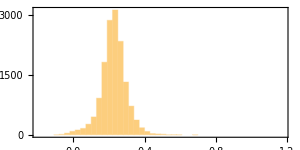
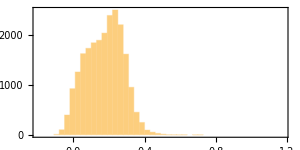

```mathematica
Row[{Histo[Select[Flatten[dat1,1],#[[1]]>50&][[All,2]],{-0.2,1.2,0.03},ImageSize->300],Histo[Select[Flatten[dat2,1],#[[1]]>50&][[All,2]],{-0.2,1.2,0.03},ImageSize->300]}]
```

FFastFLIM

```mathematica
?FFastFLIM
```

FastFLIM[routes, t_0, i_1i_2, {SubscriptBox[τ, 1], SubscriptBox[τ, 2]}, opts] or
FastFLIM[routes, t_0, i_1i_2, {SubscriptBox[τ, 1], SubscriptBox[τ, 2]}, frame, opts]
return data and and an image resulting from a fast FLIM calculation, where for each pixel the mean of the photon micro times minus t_0 is determined.
Example:
{flimdata, flimimage} == FFastFLIM[ {1,0,0,1,0,0}, t_0, i_1i_2, {SubscriptBox[τ, 1], SubscriptBox[τ, 2]}, opts]
flimdata is an array of {intensity, mean arrival time} pairs for each pixel.
i_1i_2 and {SubscriptBox[τ, 1], SubscriptBox[τ, 2]} define the brightness and hue range as described in FScanImage.
t_0 is subtracted from all mean micro times. 
The graphical output can be modified with the options of Graphics.

```mathematica
SetDirectory[$FreticaExamples];
FOpenTTTR["Area_2.ht3"]
```

1

```mathematica
FLifeTimeHisto[FRoutes->{1,2,3,4},FPhotonData->All]
```

-Graphics-

```mathematica
SetDirectory[$FreticaExamples];


route={1,1,0,0,0,0};
t0=4.6;
irange={5,15};
trange={1,5};
FOpenTTTR["Area_1.ht3"];//AbsoluteTiming
{dat1,pl1}=FFastFLIM[route,t0,irange,trange];//AbsoluteTiming
FOpenTTTR["Area_2.ht3"];//AbsoluteTiming
{dat2,pl2}=FFastFLIM[route,t0,irange,trange];//AbsoluteTiming
Row[{pl1,pl2}]
legend=FScanImageColorLegend[irange,trange,FScanImageColorLegend->"tau",FrameLabel->{"ns","counts"}];
```

{0.862354,Null}

{0.626536,Null}

{0.804044,Null}

{0.621226,Null}

-Graphics-

```mathematica
Row[{Histo2D[Reverse/@Flatten[dat1,1],{1,6,0.1},{50,700,20},PlotRange->All,FrameLabel->{"τ (ns)","intensity"},ImageSize->300],Histo2D[Reverse/@Flatten[dat2,1],{1,6,0.1},{50,700,20},PlotRange->All,FrameLabel->{"τ (ns)","intensity"},ImageSize->300]}]
```

-Graphics-

#### Select bursts from image coordinates

```mathematica
poly={{54.29,45.07},{57.21,40.69},{57.21,37.05},{53.56,36.8},{50.4,37.05},{47.73,40.45},{48.7,43.61},{51.13,44.83},{53.32,45.31}};
```

```mathematica
Show[pl2,Graphics[{Purple,Line[poly]}]]
```

-Graphics-

```mathematica
FFindBurstsFromTimeBinnedData[1,40,0,100,FCombineContiguousBins->False]
```

19169

```mathematica
select[x_]:=x≠{}&& IsInPolygonQ[x[[2]],poly]
```

```mathematica
FGetScanImageCoordinatesFromTime[50.4]
```

{1,{24.7703,84.1643}}

```mathematica
?FGetScanImageCoordinatesFromTime
```

```mathematica
FSelectBursts[{FGetScanImageCoordinatesFromTime[("EndTime"+"StartTime")/2]},select[#[[1]]]&]
```

1

```mathematica
bl=FGetFromBurstList[FGetScanImageCoordinatesFromTime[Mean[{"StartTime","EndTime"}]],FBurstData->FSelectedBursts];
bl//Length
```

289

```mathematica
Show[pl2,Graphics[{Purple,Point/@bl[[All,2]]}],Graphics[{Pink,Line[poly]}]]
```

-Graphics-

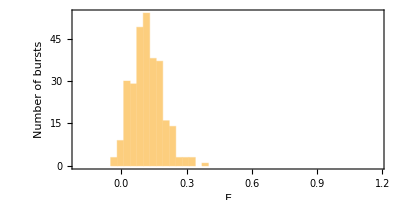

```mathematica
FParamHisto["E",{-0.2,1.2,0.03},FBurstData->FSelectedBursts]
```

| Related Guides
▪Fretica